```mathematica
m=4.8*^-26;
T=294.15;
k=1.38*^-23;
vconst=-27.7778;
```

```mathematica
f[v_]:=4*Pi*(m/(2*Pi*k*T))^(3/2)*v^2*Exp[(-m*v^2)/(2*k*T)]
```

```mathematica
ff[vc_]:=4*Pi*(m/(2*Pi*k*T))^(3/2)*(vc+vconst)^2*Exp[(-m*(vc+vconst)^2)/(2*k*T)]
fff[vc1_,vc2_,vc3_]:=4*Pi*(m/(2*Pi*k*T))^(3/2)*((vc1+vconst)^2+vc2^2+vc3^2)*Exp[(-m*((vc1+vconst)^2+vc2^2+vc3^2))/(2*k*T)]
```

```mathematica
Integrate[f[x],{x,1000,Infinity}]
```

0.00800812

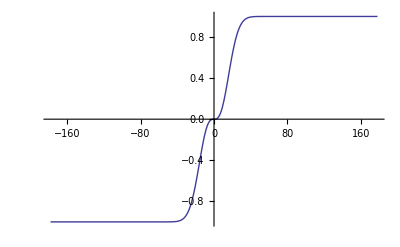

```mathematica
Plot[0.0005588887963977092 (-126.78750000000001 ⅇ^(-0.003943606428078478 x^2) x+1789.2647096264081 Erf[0.06279814032340827 x]),{x,-178.28796147540086,178.28796147540086}]
```

```mathematica
xx=2;
0.0005588887963977092 (-126.78750000000001 ⅇ^(-0.003943606428078478 xx^2) xx+1789.2647096264081 Erf[0.06279814032340827 xx])
```

0.00147634

Plot::optx: Unknown option AxisLabel → {"Velcity in [m/s]", "Fraction of Particles"} in Plot[f[v], {v, 0, 1500}, AxisLabel → {"Velcity in [m/s]", "Fraction of Particles"}].

Plot[f[v],{v,0,1500},AxisLabel→{Velcity in [m/s],Fraction of Particles}]

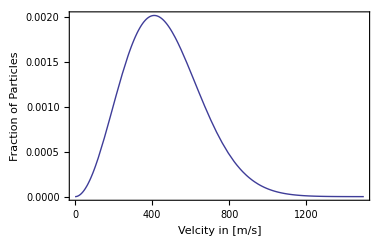

```mathematica
Plot[f[v],{v,0,1500},AxisLabel->{"Velcity in [m/s]","Fraction of Particles"}]
```

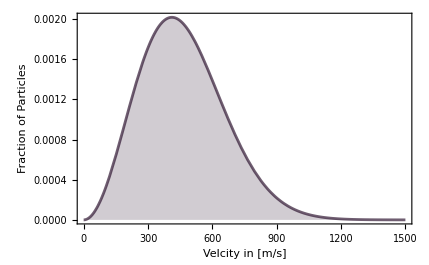

```mathematica
Plot[f[v],{v,0,1500},PlotStyle->Directive[RGBColor[0.11,0.,0.12],Opacity[0.63],AbsoluteThickness[2.]],Frame->True,FrameLabel->{"Velcity in [m/s]","Fraction of Particles"},Filling->Axis]
```

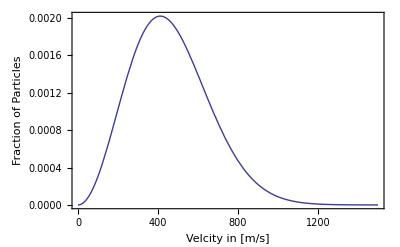

```mathematica
Show[%76,AxesStyle->Black]
```

```mathematica
IntF[xx_]:=0.0005588887963977092 (-126.78750000000001 ⅇ^(-0.003943606428078478 xx^2) xx+1789.2647096264081 Erf[0.06279814032340827 xx])
```

$Failed

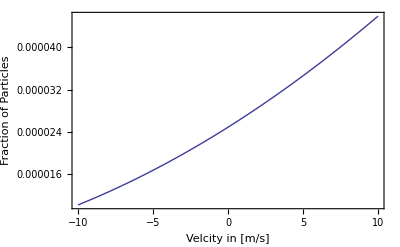

```mathematica
Plot[ff[v],{v,-10,10},Frame->True,FrameLabel->{"Velcity in [m/s]","Fraction of Particles"}]
```

```mathematica
Integrate[fff[x1,x2,x3],{x1,1000,Infinity},{x2,1000,Infinity},{x3,1000,Infinity}]
```

0.00152025

```mathematica
Integrate[ff[xy],{xy,1000,Infinity}]
```

0.0108064

```mathematica
Plot[fff[x1,x2,x3],{x1,0,1500},{x2,0,1500},{x3,0,1500}]
```

Plot::nonopt: Options expected (instead of {x3, 0, 1500}) beyond position 2 in Plot[fff[x1, x2, x3], {x1, 0, 1500}, {x2, 0, 1500}, {x3, 0, 1500}]. An option must be a rule or a list of rules.

```mathematica
Plot[fff[x1,1,1],{x1,0,1500},{x2,0,1500}]
```

Plot::nonopt: Options expected (instead of {x2, 0, 1500}) beyond position 2 in Plot[fff[x1, 1, 1], {x1, 0, 1500}, {x2, 0, 1500}]. An option must be a rule or a list of rules.

```mathematica
Plot[{f[x1],fff[x1,1,1]},{x1,0,1500}Frame->True,FrameLabel->{"Velcity in [m/s]","Fraction of Particles"}, PlotLegends->{"Original","Car"}]
```

Visualization`Core`Plot::optrs: Option specification {x1, 0, 1500}\ Frame → True in System`ProtoPlotDump`functions$98143, Mesh → None, Exclusions → Automatic, PlotPoints → 50, « 16 », GridLinesStyle → Directive[InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[GrayLevel[0.5`, 0.4`], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, GrayLevel[0.33333333333333337`, 0.4`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[ is not a rule for a symbol or string.

```mathematica
Rasterize[Plot[{f[x1],fff[x1,1,1]},{x1,0,1500} ,AxesLabel->{"Velcity in [m/s]","Fraction of Particles"},PlotLegends->{"Original","Car Frame"},Filling->Axis, ImageSize->Large],RasterSize->800]
```

-Graphics-